```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
```

## Part I

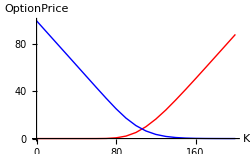

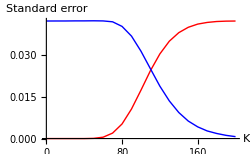

```mathematica
strikeput=ReadList["strike_put.dat",{Number,Number,Number}];
strikecall=ReadList["strike_call.dat",{Number,Number,Number}];
ErrorListPlot[{strikeput,strikecall},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"K","OptionPrice"},ImageSize->250]
ListPlot[{Drop[strikeput,None,{2}],Drop[strikecall,None,{2}]},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"K","Standard error"},ImageSize->250]
```

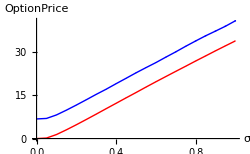

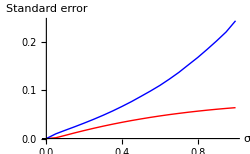

```mathematica
volput=ReadList["vol_put.dat",{Number,Number,Number}];
volcall=ReadList["vol_call.dat",{Number,Number,Number}];
ErrorListPlot[{volput,volcall},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"σ","OptionPrice"},ImageSize->250]
ListPlot[{Drop[volput,None,{2}],Drop[volcall,None,{2}]},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"σ","Standard error"},ImageSize->250]
```

## Part III

-Graphics-

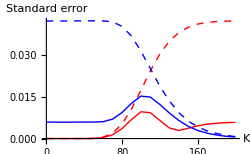

```mathematica
strikeput2=ReadList["strike_put_anti.dat",{Number,Number,Number}];
strikecall2=ReadList["strike_call_anti.dat",{Number,Number,Number}];
ErrorListPlot[{strikeput,strikecall},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"K","OptionPrice"},ImageSize->250]
Show[ListPlot[{Drop[strikeput,None,{2}],Drop[strikecall,None,{2}]},Joined->True,PlotStyle->{{Dashed,Red},{Dashed,Blue}},AxesLabel->{"K","Standard error"},ImageSize->250],ListPlot[{Drop[strikeput2,None,{2}],Drop[strikecall2,None,{2}]},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"K","Standard error"},ImageSize->250]]
```

-Graphics-

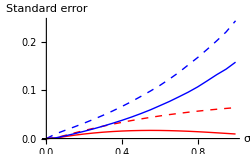

```mathematica
volput2=ReadList["vol_put_anti.dat",{Number,Number,Number}];
volcall2=ReadList["vol_call_anti.dat",{Number,Number,Number}];
ErrorListPlot[{volput,volcall},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"σ","OptionPrice"},ImageSize->250]
Show[ListPlot[{Drop[volput,None,{2}],Drop[volcall,None,{2}]},Joined->True,PlotStyle->{{Dashed,Red},{Dashed,Blue}},AxesLabel->{"σ","Standard error"},ImageSize->250],ListPlot[{Drop[volput2,None,{2}],Drop[volcall2,None,{2}]},Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"σ","Standard error"},ImageSize->250]]
```

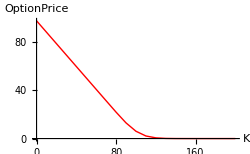

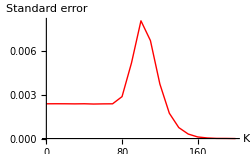

```mathematica
asianstrike = ReadList["strike_call_asian.dat",{Number,Number,Number}];
ErrorListPlot[asianstrike,Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"K","OptionPrice"},ImageSize->250]
ListPlot[Drop[asianstrike,None,{2}],Joined->True,PlotStyle->{Thick,Red},AxesLabel->{"K","Standard error"},ImageSize->250]
```

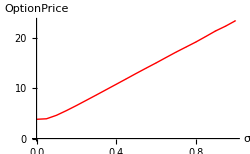

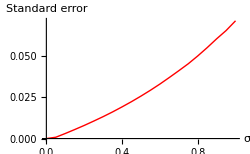

```mathematica
asianvol = ReadList["vol_call_asian.dat",{Number,Number,Number}];
ErrorListPlot[asianvol,Joined->True,PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"σ","OptionPrice"},ImageSize->250]
ListPlot[Drop[asianvol,None,{2}],Joined->True,PlotStyle->{Thick,Red},AxesLabel->{"σ","Standard error"},ImageSize->250]
```

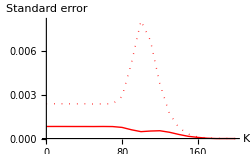

```mathematica
strikecall3=ReadList["strike_call_asian_variate.dat",{Number,Number,Number}];
Show[ListPlot[{Drop[asianstrike,None,{2}],Drop[strikecall3,None,{2}]},Joined->True,PlotStyle->{{Dotted,Red},{Thick,Red}},AxesLabel->{"K","Standard error"},ImageSize->250]]
```

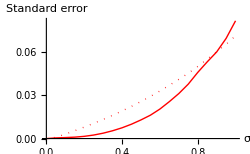

```mathematica
volcall3=ReadList["vol_call_asian_variate.dat",{Number,Number,Number}];
Show[ListPlot[{Drop[asianvol,None,{2}],Drop[volcall3,None,{2}]},Joined->True,PlotStyle->{{Dotted,Red},{Thick,Red}},AxesLabel->{"σ","Standard error"},ImageSize->250]]
```